```mathematica
values={10113,10217,9456,9692,10064,9693,9654,9760,9774,10121,10030,9833,9861,9678,9685,9767,9568,9728,9758,10288,10145,9640,10218,9517,9805,10015,9469,9611,9643,9659,9842,9753,9589,9741,9709,9621,9958,9745,9910,9441,9985,9812,10080,10024,10081,9784,10052,10020,9764,9900,9636,9509,9483,9872,9723,10050,10123,9970,10023,9813,9621,9683,10141,9740,9986,9988,9629,10003,10080,9744,9678,10030,9705,9972,9654,9891,9689,9594,10140,10162,9834,9903,10028,9900,9810,9905,9611,9734,9804,9592,9714,10011,10153,9717,9953,9937,9669,9936,9757,9854,9747,10016,9741,9592,9968,9814,9751,10237,9936,9557,9880,9919,9642,9956,9756,9714,10138,9916,9879,9857,9736,9739,9850,9964,9667,10242,10127,9728,10309,9922,9429,9803,9961,9738,9951,9664,9895,9782,10104,9575,9961,9987,9756,9594,9892,9633,9933,9931,9963,10016,10179,10135,9466,10164,9853,9795,9779,9774,9635,9809,9663,9819,10286,9989,9833,9989,9852,9663,9868,9871,9548,9777,9824,9819,9770,10093,9783,10008,9815,9538,9570,9863,9845,9592,9922,9781,9880,9888,9645,9752,9965,9647,9919,9877,9742,9788,9837,10133,9947,10100,10012,10000,9793,9511,9619,9978,9748,9894,9899,9812,10115,9780,9763,9684,9771,9711,9823,9986}
```

{10113,10217,9456,9692,10064,9693,9654,9760,9774,10121,10030,9833,9861,9678,9685,9767,9568,9728,9758,10288,10145,9640,10218,9517,9805,10015,9469,9611,9643,9659,9842,9753,9589,9741,9709,9621,9958,9745,9910,9441,9985,9812,10080,10024,10081,9784,10052,10020,9764,9900,9636,9509,9483,9872,9723,10050,10123,9970,10023,9813,9621,9683,10141,9740,9986,9988,9629,10003,10080,9744,9678,10030,9705,9972,9654,9891,9689,9594,10140,10162,9834,9903,10028,9900,9810,9905,9611,9734,9804,9592,9714,10011,10153,9717,9953,9937,9669,9936,9757,9854,9747,10016,9741,9592,9968,9814,9751,10237,9936,9557,9880,9919,9642,9956,9756,9714,10138,9916,9879,9857,9736,9739,9850,9964,9667,10242,10127,9728,10309,9922,9429,9803,9961,9738,9951,9664,9895,9782,10104,9575,9961,9987,9756,9594,9892,9633,9933,9931,9963,10016,10179,10135,9466,10164,9853,9795,9779,9774,9635,9809,9663,9819,10286,9989,9833,9989,9852,9663,9868,9871,9548,9777,9824,9819,9770,10093,9783,10008,9815,9538,9570,9863,9845,9592,9922,9781,9880,9888,9645,9752,9965,9647,9919,9877,9742,9788,9837,10133,9947,10100,10012,10000,9793,9511,9619,9978,9748,9894,9899,9812,10115,9780,9763,9684,9771,9711,9823,9986}

```mathematica
ListPlot[Mean[values], Joined->True]
```

ListPlot::lpn: 2115764/215 is not a list of numbers or pairs of numbers.

ListPlot[2115764/215,Joined→True]

```mathematica
SectorChart[Table[{Mean[values],values[[i]]},{i,1,Length[values]}],SectorOrigin->{Automatic,Min[values]}]
```

-Graphics-

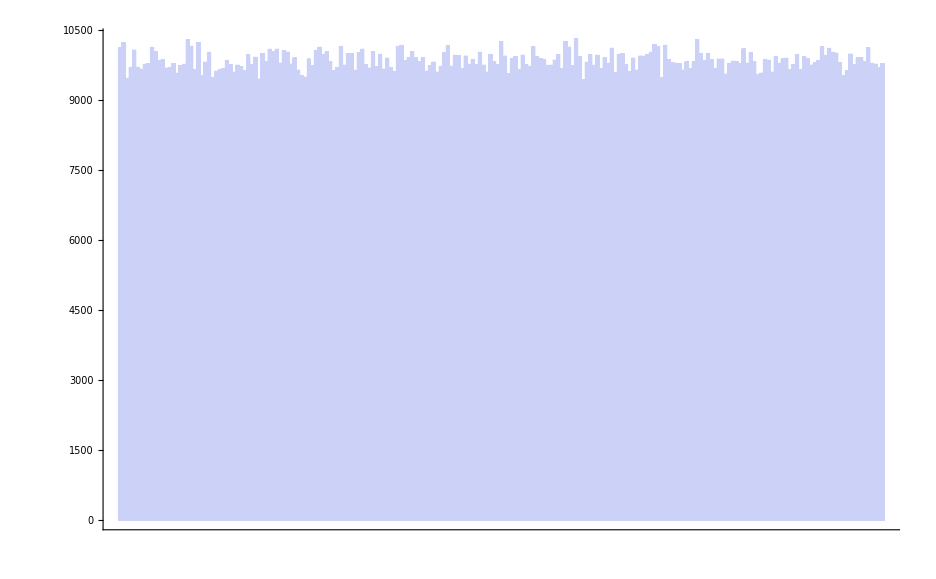

```mathematica
BarChart[values]
```

```mathematica
N[Skewness[values]]
```

0.181893

```mathematica
N[Mean[values]]
```

9840.76

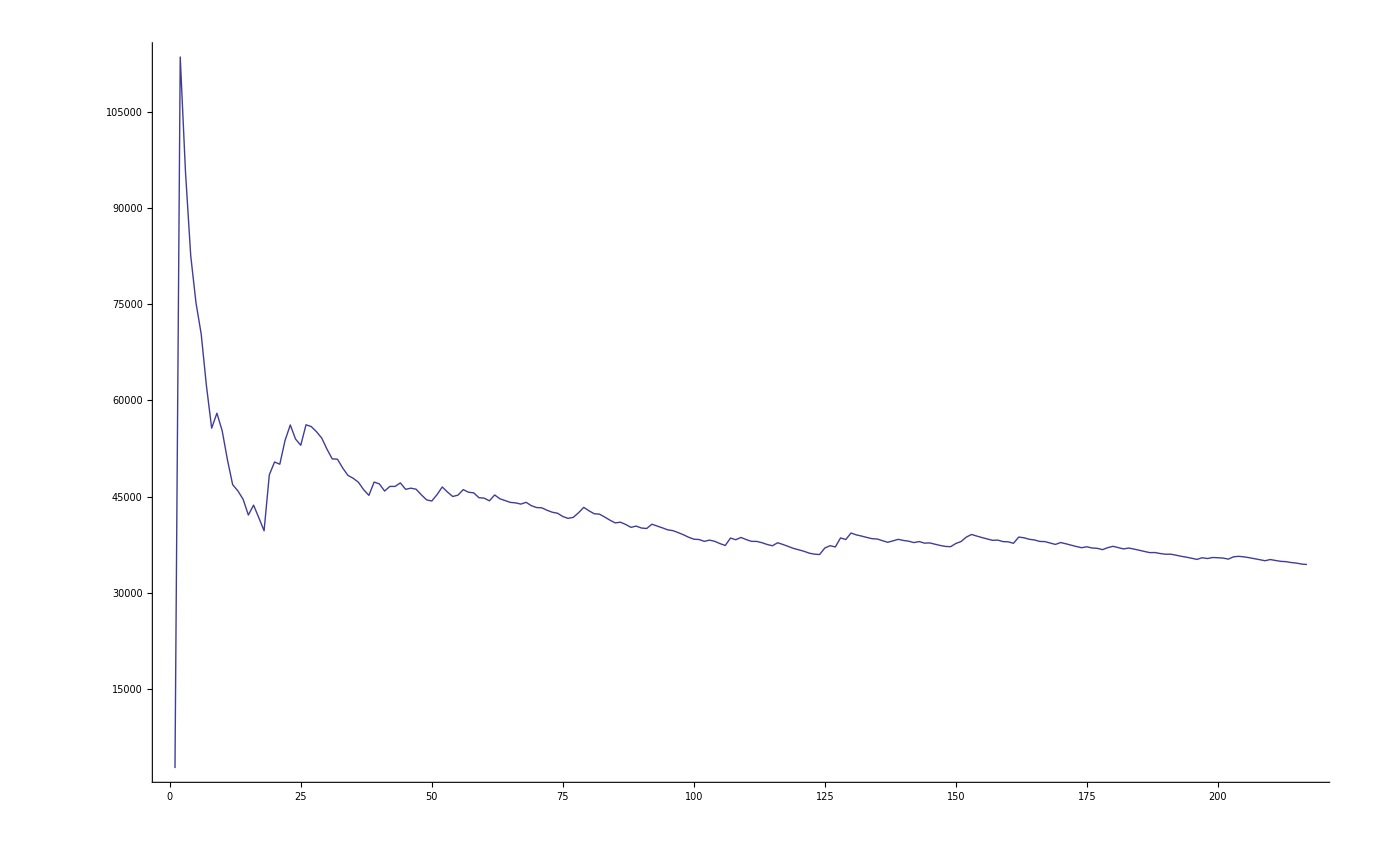

```mathematica
ListPlot[Table[CentralMoment[Take[values,i],2],{i,2,Length[values]}], Joined->True]
```

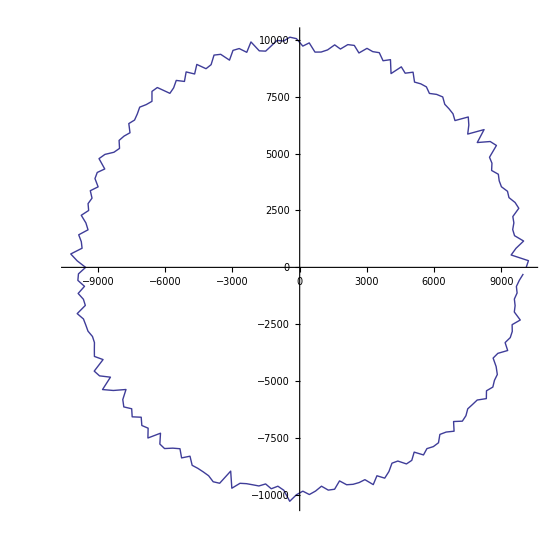

```mathematica
ListPolarPlot[values, Joined->True]
```

```mathematica
PieChart[values]
```

-Graphics-

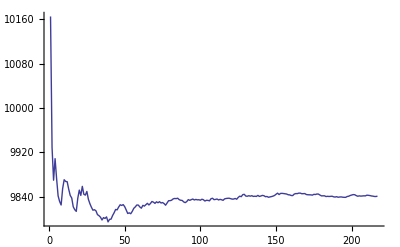

```mathematica
ListPlot[Table[Mean[Take[values,i]],{i,2,Length[values]}], Joined->True]
```

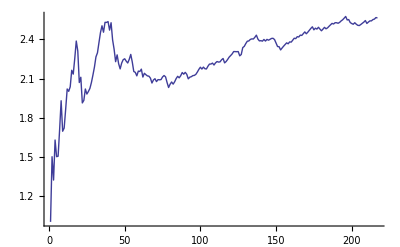

```mathematica
ListPlot[Table[Kurtosis[Take[values,i]],{i,2,Length[values]}], Joined->True]
```

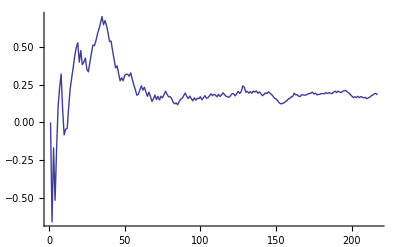

```mathematica
ListPlot[Table[Skewness[Take[values,i]],{i,2,Length[values]}], Joined->True]
```

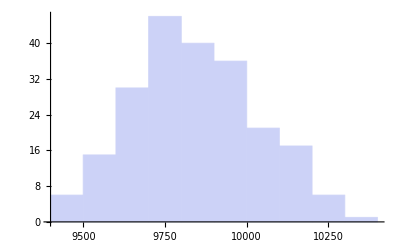

```mathematica
Histogram[values]
```

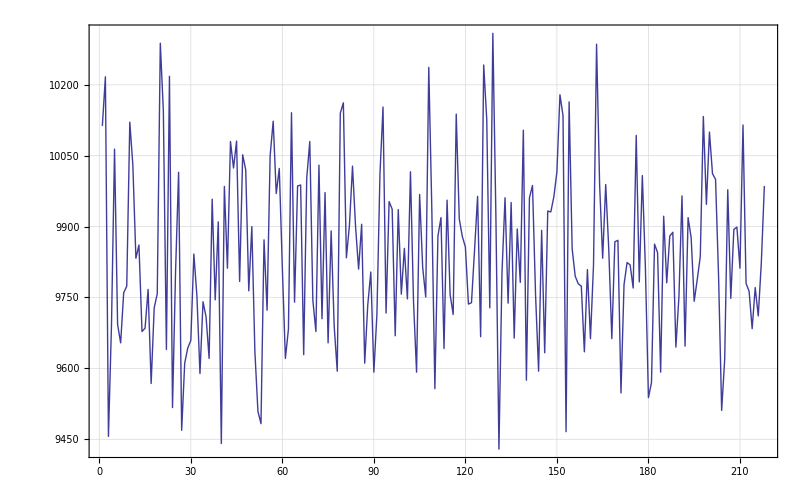

```mathematica
ListPlot[values, Joined->True, GridLines->Automatic, Frame->True]
```

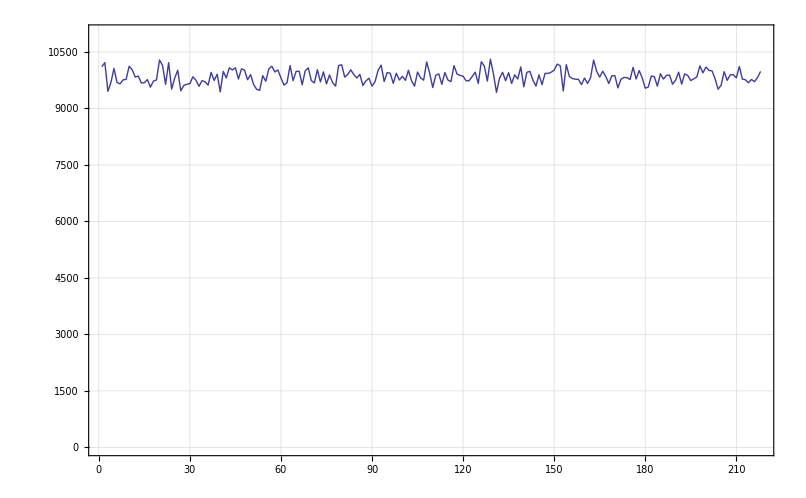

```mathematica
ListPlot[values, Joined->True, GridLines->Automatic, Frame->True, PlotRange->{Automatic,{0,11000}}]
```

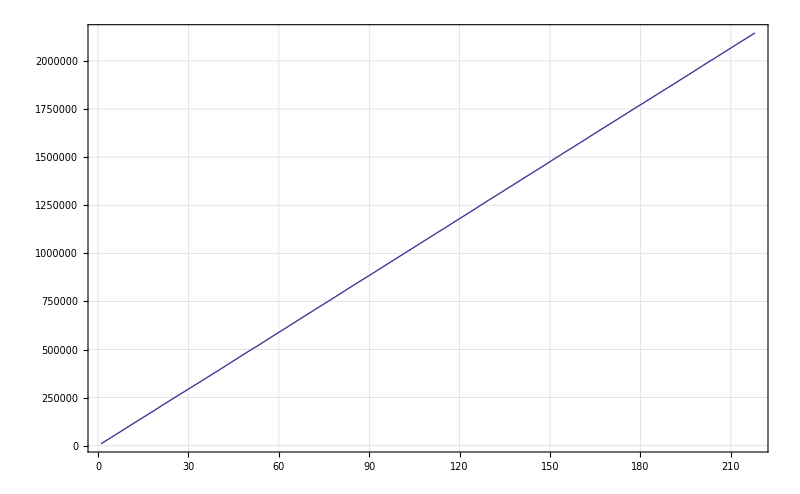

```mathematica
ListPlot[Accumulate[values], Joined->True, GridLines->Automatic, Frame->True]
```

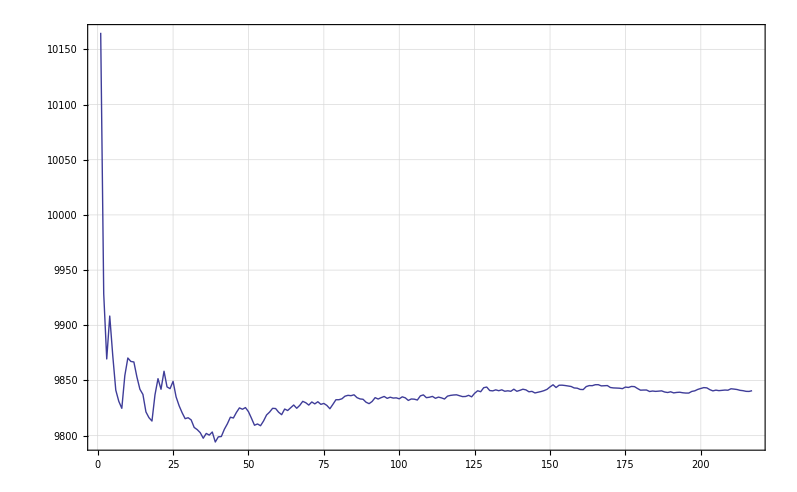

```mathematica
ListPlot[Table[Mean[Take[values,i]],{i,2,Length[values]}], Joined->True, GridLines->Automatic, Frame->True]
```

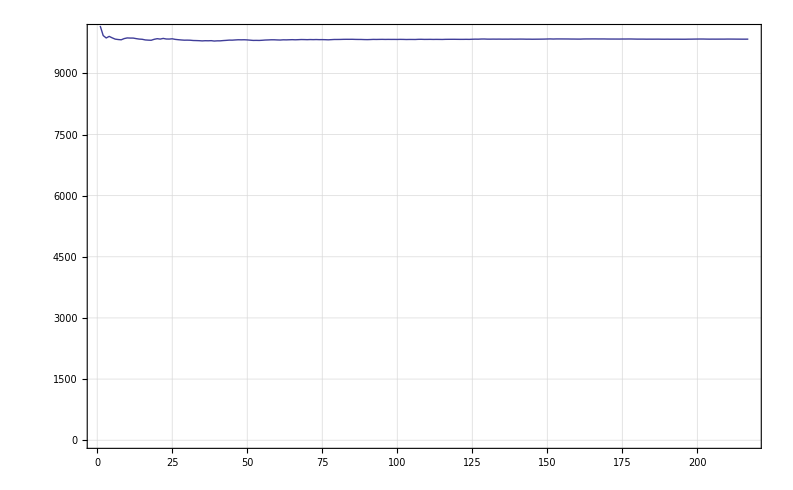

```mathematica
ListPlot[Table[Mean[Take[values,i]],{i,2,Length[values]}], Joined->True, GridLines->Automatic, Frame->True,PlotRange->{Automatic,{0,10000}}]
```

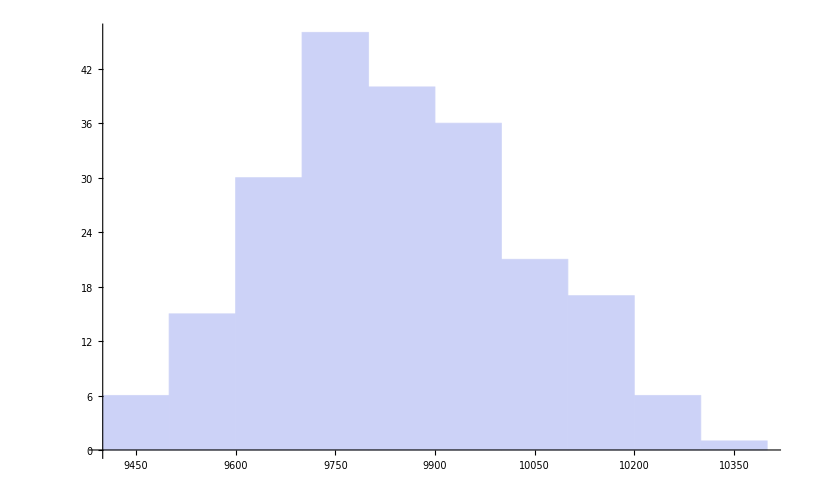

```mathematica
Histogram[values]
```

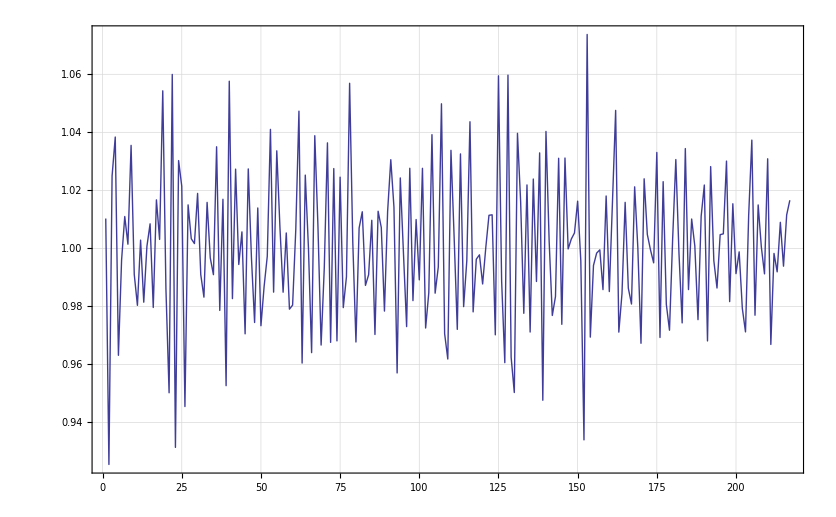

```mathematica
ListPlot[Ratios[values], Joined->True, GridLines->Automatic, Frame->True]
```

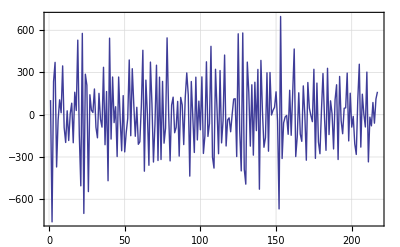

```mathematica
ListPlot[Differences[values], Joined->True, GridLines->Automatic, Frame->True]
```